```mathematica
Ps[x_]:= Exp[0.4(x-0.4)^2-0.08 x^4]
```

```mathematica
Qs[x_]:= 2.5 Exp[-x^2/4]
```

```mathematica
ϕ[x_]:=4Sin[x]
```

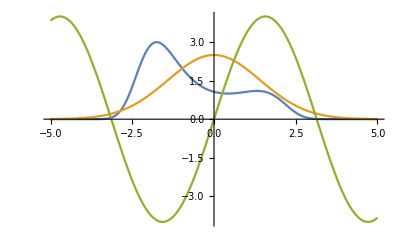

```mathematica
Plot[{Ps[x],Qs[x],ϕ[x]},{x,-5,5}]
```

```mathematica
∫_-10^10 Ps[x]ϕ[x]ⅆx
```

∫_-10^10 4 ⅇ^(0.4 (-0.4+x)^2-0.08 x^4) Sin[x]ⅆx

```mathematica
NIntegrate[Ps[x]ϕ[x],{x,-10,10}]
```

-10.3541

```mathematica
NIntegrate[Ps[x]ϕ[x],{x,-20,20}]
```

-10.3541

```mathematica
Abs[-10.354127061644693]
```

10.3541

```mathematica
NIntegrate[Ps[x],{x,-20,20}]
```

7.85218

```mathematica
-10.354127061644693/7.852178178866329
```

```mathematica
-1.3186311907073391}
```